```mathematica
y[x_] = ComplexExpand[I * (x+I)/(x - I)]
```

```mathematica
-(2 x)/(1+x^2)+ⅈ (-1/(1+x^2)+x^2/(1+x^2))

Expand[((2 x)/(1+x^2))^2 + ((-1/(1+x^2)+x^2/(1+x^2)))^2]
```

-(2 x)/(1+x^2)+ⅈ (-1/(1+x^2)+x^2/(1+x^2))

1/((1+x^2)^2)+(2 x^2)/((1+x^2)^2)+x^4/((1+x^2)^2)

```mathematica
D[-(2 x)/(1+x^2)+ⅈ (-1/(1+x^2)+x^2/(1+x^2)),x]
```

```mathematica
(4 x^2)/((1+x^2)^2)-2/(1+x^2)+ⅈ ((2 x)/((1+x^2)^2)-(2 x^3)/((1+x^2)^2)+(2 x)/(1+x^2))

((4 x^2)/((1+x^2)^2)-2/(1+x^2)+ⅈ ((2 x)/((1+x^2)^2)-(2 x^3)/((1+x^2)^2)+(2 x)/(1+x^2)) )*(I*(x - I)/(x+I))
```

(4 x^2)/((1+x^2)^2)-2/(1+x^2)+ⅈ ((2 x)/((1+x^2)^2)-(2 x^3)/((1+x^2)^2)+(2 x)/(1+x^2))

(ⅈ (-ⅈ+x) ((4 x^2)/((1+x^2)^2)-2/(1+x^2)+ⅈ ((2 x)/((1+x^2)^2)-(2 x^3)/((1+x^2)^2)+(2 x)/(1+x^2))))/(ⅈ+x)

```mathematica
(ⅈ (-ⅈ+x) ((4 x^2)/((1+x^2)^2)-2/(1+x^2)+ⅈ ((2 x)/((1+x^2)^2)-(2 x^3)/((1+x^2)^2)+(2 x)/(1+x^2))))/(ⅈ+x)
ComplexExpand[%]
```

(ⅈ (-ⅈ+x) ((4 x^2)/((1+x^2)^2)-2/(1+x^2)+ⅈ ((2 x)/((1+x^2)^2)-(2 x^3)/((1+x^2)^2)+(2 x)/(1+x^2))))/(ⅈ+x)

(2 x)/((1+x^2)^3)+(4 x^3)/((1+x^2)^3)+(2 x^5)/((1+x^2)^3)-(2 x)/((1+x^2)^2)-(2 x^3)/((1+x^2)^2)+ⅈ (2/((1+x^2)^2)+(2 x^2)/((1+x^2)^2))

```mathematica
Integrate[%, {x, -Infinity, Infinity}]
```

2 ⅈ π

```mathematica
ComplexContourPlot[-2x/(x^2+1) + I*((x^2-1)/(x^2+1)), {x, -10 + 0* I,10 + 0*I}]
```

ComplexContourPlot::plld: Corners for x in {x,-10,10} must have distinct machine-precision real and imaginary parts.

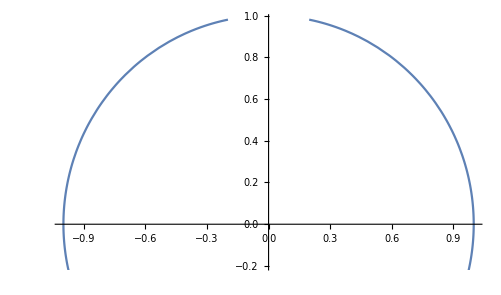

```mathematica
ParametricPlot[{-(2 x)/(x^2+1),(x^2-1)/(x^2+1)},{x,-10,10}]
```

```mathematica
Series[(Sinh[z] - z)/z^4, {z , 0, 5}]
```

1/(6 z)+z/120+z^3/5040+z^5/362880+O[z]^6

```mathematica
f[z_] = Sinh[z]/ (z + Pi*I)^2

D[f[z],z]
% /. z->Pi * I
```

Sinh[z]/(ⅈ π+z)^2

Cosh[z]/(ⅈ π+z)^2-(2 Sinh[z])/(ⅈ π+z)^3

```mathematica
1/(4 π^2)


(5!)^2 /(6(7!))
```

1/(4 π^2)

10/21

```mathematica
5/756


Series[z^4/(6z + z^3 - 6Sinh[z]),{z,0,4}]
```

5/756

-20/z+(10 z)/21-(25 z^3)/5292+O[z]^5

```mathematica
Rot3[z_] = Exp[I * Pi * (z/3)]

(1 - Rot3[2])(Rot3[1] - Rot3[3])

Simplify[%]
```

ⅇ^((ⅈ π z)/3)

(1+ⅇ^((ⅈ π)/3)) (1-ⅇ^((2 ⅈ π)/3))

3

```mathematica
Rot[z_] = Exp[I * Pi * (z/6)]
```

ⅇ^((ⅈ π z)/6)

```mathematica
1/((Rot[1]- Rot[3])(Rot[1]- Rot[5])(Rot[1]- Rot[7])(Rot[1]- Rot[9])(1 - Rot[2]))
```

```mathematica
1/((-ⅈ+ⅇ^((ⅈ π)/6)) (ⅈ+ⅇ^((ⅈ π)/6)) (1-ⅇ^((ⅈ π)/3)) (ⅇ^((ⅈ π)/6)-ⅇ^(-(5 ⅈ π)/6)) (ⅇ^((ⅈ π)/6)-ⅇ^((5 ⅈ π)/6)))

Simplify[%]
```

1/((-ⅈ+ⅇ^((ⅈ π)/6)) (ⅈ+ⅇ^((ⅈ π)/6)) (1-ⅇ^((ⅈ π)/3)) (ⅇ^((ⅈ π)/6)-ⅇ^(-(5 ⅈ π)/6)) (ⅇ^((ⅈ π)/6)-ⅇ^((5 ⅈ π)/6)))

1/6

```mathematica
(2*(Rot[1])^2 - 1)/((Rot[1]- Rot[3])(Rot[1]- Rot[5])(Rot[1]- Rot[7])(Rot[1]- Rot[9])(Rot[1]- Rot[11]) )
```

(-1+2 ⅇ^((ⅈ π)/3))/((-ⅈ+ⅇ^((ⅈ π)/6)) (ⅈ+ⅇ^((ⅈ π)/6)) (-ⅇ^(-(ⅈ π)/6)+ⅇ^((ⅈ π)/6)) (ⅇ^((ⅈ π)/6)-ⅇ^(-(5 ⅈ π)/6)) (ⅇ^((ⅈ π)/6)-ⅇ^((5 ⅈ π)/6)))

```mathematica
Simplify[%]
```

(3-ⅈ √3)/(6 ⅈ+6 √3)

```mathematica
(2*(Rot[3])^2 - 1)/((Rot[3]- Rot[1])(Rot[3]- Rot[5])(Rot[3]- Rot[7])(Rot[3]- Rot[9])(Rot[3]- Rot[11]) )
```

(3 ⅈ)/(2 (ⅈ-ⅇ^(-(ⅈ π)/6)) (ⅈ-ⅇ^((ⅈ π)/6)) (ⅈ-ⅇ^(-(5 ⅈ π)/6)) (ⅈ-ⅇ^((5 ⅈ π)/6)))

```mathematica
Simplify[%]
```

ⅈ/2

```mathematica
(2*(Rot[5])^2 - 1)/((Rot[5]- Rot[1])(Rot[5]- Rot[3])(Rot[5]- Rot[7])(Rot[5]- Rot[9])(Rot[5]- Rot[11]) )
```

(-1+2 ⅇ^(-(ⅈ π)/3))/((-ⅈ+ⅇ^((5 ⅈ π)/6)) (ⅈ+ⅇ^((5 ⅈ π)/6)) (-ⅇ^(-(ⅈ π)/6)+ⅇ^((5 ⅈ π)/6)) (-ⅇ^((ⅈ π)/6)+ⅇ^((5 ⅈ π)/6)) (-ⅇ^(-(5 ⅈ π)/6)+ⅇ^((5 ⅈ π)/6)))

```mathematica
Simplify[%]
```

1/6 (-2 ⅈ+(-1)^(5/6))

```mathematica
%97 + %99+ %101
```

```mathematica
ⅈ/2+1/6 (-2 ⅈ+(-1)^(5/6))+(3-ⅈ √3)/(6 ⅈ+6 √3)
```

ⅈ/2+1/6 (-2 ⅈ+(-1)^(5/6))+(3-ⅈ √3)/(6 ⅈ+6 √3)

```mathematica
Simplify[%]
```

0

```mathematica
2 Pi I  %
```

16/3 ⅈ i π^3

```mathematica
Integrate[(2x^2  - 1)/(x^6 + 1), {x, 0, Infinity}]
```

0

```mathematica
Series[Tan[z],{z,-Pi/2,6}]
```

```mathematica
-1/(z+π/2)+1/3 (z+π/2)+1/45 (z+π/2)^3+2/945 (z+π/2)^5+O[z+π/2]^7


Integrate[Tan[3e^{I * z}]*(3 I e^{I * z}),{z,0, 2 * Pi}]
```

-1/(z+π/2)+1/3 (z+π/2)+1/45 (z+π/2)^3+2/945 (z+π/2)^5+O[z+π/2]^7

{ConditionalExpression[(ⅈ (π-ⅈ Log[-Cos[3]]+ⅈ Log[Cos[3 e^(2 ⅈ π)]]))/Log[e], Im[Log[e]]>0]}

```mathematica
((1- Rot))
```